# To learn, perchance to dream...

Name: Sanjit Singh Batra

Instructor: Taliesin Beynon

Wolfram Science Summer School 2012

## Homework Solution:

## The Result: 1080228952069739329181238

## The Filters:

```mathematica
runtm[rl_Integer,steps_:50]:=TuringMachine[{rl,4,4},{1,{{},0}},steps]
diff[l_]:=Table[l[[i]]-l[[i+2]],{i,1000,1020}]



linear1[l_]:=Table[l[[1000]]-i,{i,0,21}]==l[[1000;;1021]]
linear2[l_]:=Table[l[[1000]]+i,{i,0,21}]==l[[1000;;1021]]
```

```mathematica
nested5[l_]:=Module[{list,a,b,c,d,p,q,r,s,t},
list=Cases[{diff[l]},{a___,p_,q_,r_,s_,t_,b__,p_,q_,r_,s_,t_,c__,p_,q_,r_,s_,t_,d___}:>{{a},{p},{q},{r},{s},{t},{b},{c},{d}}];
(Length[{p}]*Length[{q}]*Length[{r}]*Length[{s}]*Length[{t}]==1) &&(Length[list]>0)
]
analysis5[l_]:=Cases[{diff[l]},{a___,p_,q_,r_,s_,t_,b__,p_,q_,r_,s_,t_,c__,p_,q_,r_,s_,t_,d___}:>{{a},{p},{q},{r},{s},{t},{b},{c},{d}}];
```

```mathematica
nested6[l_]:=Module[{list,a,b,c,d,p,q,r,s,t,u},
list=Cases[{diff[l]},{a___,p_,q_,r_,s_,t_,u_,b__,p_,q_,r_,s_,t_,u_,c___}:>{{a},{p},{q},{r},{s},{t},{u},{b},{c}}];
(Length[{p}]*Length[{q}]*Length[{r}]*Length[{s}]*Length[{t}]*Length[{u}]==1) &&(Length[list]>0)
]
analysis6[l_]:=Cases[{diff[l]},{a___,p_,q_,r_,s_,t_,u_,b__,p_,q_,r_,s_,t_,u_,c___}:>{{a},{p},{q},{r},{s},{t},{u},{b},{c}}];
```

```mathematica
diff2[l_]:=Table[headpos[[i]]-headpos[[i+2]],{i,1000,1023}]
```

```mathematica
nestedlong3[l_]:=Module[{a,p,b,d,list},
list=Cases[{diff2[l]},{a___,Longest[p__],b___,Longest[p__],b___Longest[p__],d___}:>{{a},{p},{b}{d}}];
(Length[list]>0)&&(Length[list[[1]][[2]]]≥5)
]
analysislong3[l_]:=Cases[{diff2[l]},{a___,Longest[p__],b___,Longest[p__],b___,Longest[p__],d___}:>{{a},{p},{b},{d}}];
```

```mathematica
nestedlong2[l_]:=Module[{a,p,d,list},
list=Cases[{diff2[l]},{a___,Longest[p__],Longest[p__],d___}:>{{a},{p},{d}}];
(Length[list]>0)&&(Length[list[[1]][[2]]]≥6)
]

analysislong2[l_]:=Cases[{diff2[l]},{a___,Longest[p__],Longest[p__],d___}:>{{a},{p},{d}}];
```

```mathematica
nested1[l_]:=Module[{a,b},
a=Sort[ DeleteDuplicates[diff[l]]];
b=Plus@@diff[l];
(a=={-1,1}||a=={0,2}||a=={-1,0}||a=={0,1}||a=={-2,0}||a=={0})
]
```

## The Process:

```mathematica
rule1=RandomInteger[{10^24,10^18+10^21+10^24}];
evol=runtm[ rule1 ,5000];
headpos=evol[[All,1,2]][[5 10^2;;5 10^3]];TM5TM5
While[nested1[headpos]||linear1[headpos]||linear2[headpos]||nestedlong3[headpos],
count=0;
rule1=RandomInteger[{10^24,10^18+10^21+10^24}]+RandomInteger[count^5];
evol=runtm[ rule1 ,5000];
headpos=evol[[All,1,2]][[5 10^2;;5 10^3]];count++;];
rule1;
Sort[ DeleteDuplicates[diff[headpos]]];
analysislong3[headpos];
analysislong2[headpos];
```

TM5TM5

## The Discovery!

```mathematica
rule1=1080228952069739329181238;
evol=runtm[ rule1 ,500000];
headpos=evol[[All,1,2]][[5 10^3;;5 10^5]];
diff[headpos];

ListLinePlot[headpos,ImageSize->800,AspectRatio->1/2]
```

-Graphics-

```mathematica
history=TuringMachine[{1080228952069739329181238,4,4},{1,{{},0}},30000];
ArrayPlot[history[[All, 2]],ColorRules->{0->White,1->Green,2->Red,3->Blue},AspectRatio->GoldenRatio,ImageSize->500]
```

## Learning to Dream:

## What is a ‘Simple’ Boltzmann Machine?

A Boltzmann Machine is ‘stochastic neural network’ consisting of a network of binary units, with a defined notion of energy for the network. The state of a unit is a Bit Vector. The global Energy is defined as:

-Graphics-

Where w is the weight matrix used to represent the connection strength.
The process of finding the local minima in the Energy Distribution yields the attractors for the system. To visualize this output, a weighted colour for each state was computed by attaching each attractor to a separate colour and the weights were the frequency with which a state converged to an attractor. The states when enumerated as the Gray Code, and then mapped on to the Hilbert curve displayed the following interesting property:
States which had lesser hamming distance would tend to have similar weighted colours. And these were mapped to points in 2D that were “close” again, due to the distance preserving property of the Hilbert Curve. As a result, local neighbours in the Hilbert Curve had similar colours, as can be seen by the following demonstration:
<Demonstration>

## Can Boltzmann Machines ‘learn’?

Suppose we have a Binary image, i.e. each pixel is either 0 or 1, and suppose we were posed the problem of recognizing what object was being portrayed in the image. 

A Restricted Boltzmann Machine is a ‘stochastic neural networks’, much like a Simple Boltzmann Machine, but they differ in the fact that there are now two layers of neurons, the ‘visible’ neurons and the ‘hidden’ neurons. Also, the connections in this network form a Bipartite graph between these two layers. To make learning easier, we restrict the network so that there are no connections within the same layer. So, the network, together with the Bias units, looks like the following: 
-Graphics-

Restriced Boltzmann Machines work by updating the states of some neurons given the states of others. So, to perform learning, we compute the states for hidden neurons given the visible states, by using the logistic activation rule, which means that each activation energy is converted to a value between 0 and 1 using the Logistic function. We now compute Positive (e(i,j)) = x(i)*x(j) for each edge. Following this, after obtaining the states for the hidden neurons, we sample the reconstruction of the visible units, by repeating the procedure, but instead using the hidden neurons as the input. We now compute Negative(e(i,j)) = x(i)*x(j), for each edge.
Now, to update the weight matrix, we set:
W(i,j) = W(i,j) + ϵ *(Positive(e(i,j)) - Negative(e(i,j))) where ϵ is the learning rate. This is then repeated for all the training examples to get the ‘Learnt’ weight matrix, which can then be used for Inference.
This rule is called Contrastive Divergence, and it helps the network’s ‘hallucinations’(reconstructions) match the reality better!

## Deep Learning

The realization that one could do Machine Learning with a Restricted Boltzmann machine was very useful. But, what made this a tractable avenue was the realization that, if we stack multiple RBMs on top of one another, we could prove that the learning would be more accurate, and what’s more is that we could use this concept to make what are called Deep AutoEncoders which could be used to store very high dimension data in a compressed form without losing information, which was a very significant development.

## Explorations:

### Simple Boltzmann Machines

We simulated the functioning of a Boltzmann machine consisting of n units, in which each unit can be connected to any other and the connections are undirected. The weights of the connections are represented in the form of a weight matrix. Each unit’s state is represented by a binary unit vector. There is a defined notion of Energy of the system, and the obective was to find the states corresponding to local minima in the energy landscape. These are called attractors. The method used was to randomly update the state of a unit if doing so reduced the overall energy of the system. To visualize the basins of attraction of the system, a weighted colour scheme was used, to attach weight to each state based on how often they converged to one of the many attractors. Also, they were enumerated in the form of the Gray code, to preserve distance among them. Subsequently they were mapped to the Hilbert curve, which is distance preserving, the result of which was that, states closeby in the binary hypercube, were mapped to closeby points, and since they would tend to converge to similar attractors, the Hilbert curve had the following interesting property:
Local neighbours had similar colours!

Here is the code:

# Simple Boltzmann Machines

### Create random machine

```mathematica
RandomSeed[1];
W=RandomReal[{-100,+100},{8,8}];
Do[W[[i,i]] = 0,{i,8}];
W=W+Wᵀ;
theta=RandomReal[10,8]
```

{3.13286,3.18998,8.98395,3.27711,3.76508,4.12299,8.66598,4.36456}

### Fundamental algorithm

```mathematica
Energy[w_,θ_][s_] := θ . s - ((s . w. s)/2);
```

```mathematica
UpdateState[w_,θ_][s_]:= With[{s2 = MapAt[1-#&, s, RandomInteger[{1,Length[s]}]]},
If[Energy[w,θ][s2]<Energy[w,θ][s],s2,s]]
```

### Utility functions

```mathematica
graycode[n_]:=Map[IntegerDigits[#,2,n]&,Map[BitXor[#,Floor[#/2]]&,Range[0,2^n-1]]]
```

```mathematica
Converge[w_,θ_][state_]:=Nest[UpdateState[w,θ],state,30000]

Converge2[w_,θ_][state_]:=Module[
	{state2=state,len=Length[state], newstate,i, energy, newenergy},
	energy = θ . state - ((state . w. state)/2);
	Do[
		i = RandomInteger[{1,len}];
		newstate = state2;
		newstate[[i]] = 1 - newstate[[i]];
		newenergy = θ . newstate - ((newstate . w. newstate)/2);
		If[newenergy < energy,
			state2 = newstate;
			energy = newenergy;
		]
	,
		{300}
	];
	state2
]
```

```mathematica
FindAttractors[w_,θ_][state_] := Tally[Table[Converge2[w,θ][state],{i,40}]]
```

```mathematica
FindBasins[w_,θ_]:= {FindAttractors[w,θ][#],#}&/@graycode[Length[θ]]
```

#### Basins Of Attraction

```mathematica
basins = FindBasins[W, theta];
Length[basins]
```

256

```mathematica
The Attractors
```

```mathematica
nbrs[state_]:=Table[ReplacePart[state,i->1-state[[i]]],{i,Length[state]}]
MinimumQ[w_,θ_][state_]:=Min[Map[Energy[w,θ],nbrs[state]]] > Energy[w,θ][state];
AllAttractors[w_,θ_]:= Select[Tuples[{0,1},Length[θ]], MinimumQ[w,θ]];
att1=AllAttractors[W,theta];
att=Cases[graycode[8],Alternatives@@att1]
{{0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1},{1,1,0,1,1,1,0,0},{1,0,1,0,1,1,0,1}}
```

```mathematica
Colouring Scheme for the Hilbert Curve
```

```mathematica
blend[{x_}, {_}] := x;
blend[a_, b_]:=Blend[a,b]; 
colourmap[l_]:= Hue[(Flatten[Position[att,l]]-1.0)/(Length[att])]
weightedcolour[l_] := blend[Map[colourmap, l[[All,1]]], l[[All,2]]];
colourmap /@ att
{Hue[{0.}],Hue[{0.5}]}
```

```mathematica
Indexing
```

```mathematica
Indexpos[k_][{a_,b_}]:={a,k}
PutIndex[lis_]:=Module[{l={}},For [p=1,p<=Length[lis],p++,AppendTo[l,Indexpos[p][lis[[p]]]]];l]
```

### Hilbert Curve : 1-D =>> 2-D map

```mathematica
rot[s_,x_,y_,rx_,ry_]:=Module[ {x1=x,y1=y,tp},

If[ry==0,If[rx==1,x1=s-1-x;y1=s-1-y;];tp=x1;x1=y1;y1=tp;];
{s,x1,y1,rx,ry}
]
d2xy[n_][d_]:=Module[{rx,ry,t=d,x=0,y=0,s},
For[s=1,s<n,s*=2,rx=BitAnd[1,Floor[(t/2)]];ry=BitAnd[1,BitXor[t,rx]];
{s,x,y,rx,ry}=rot[s,x,y,rx,ry];x=x+(s*rx);y=y+(s*ry);t=Floor[t/4];
];
{x,y}
]
```

#### Execution:

```mathematica
MapHilbert[l_,n_]:= MapThread[{#1,d2xy[n][#2]}&,Transpose@l]
h={weightedcolour[#1], #2}& @@@ MapHilbert[PutIndex[basins],16];
```

```mathematica
arr=ConstantArray[0,{16,16}];
setarr[col_, {p1_,p2_}]:=arr[[1+p1,1+p2]]=col;
setarr @@@ h;
```

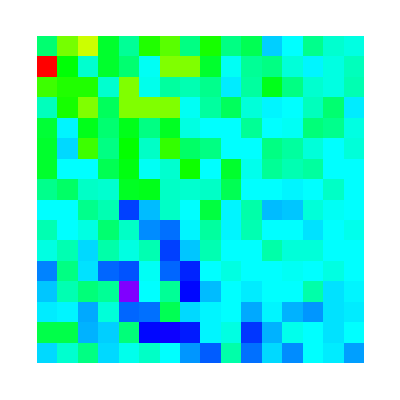

```mathematica
ArrayPlot[arr]
(*
Graphics[{PointSize[Large],Style[Point[#2],#1]&@@@h}]*)
```

### Developing intuition by visualizing

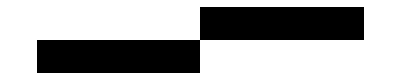
The Deep Learning setup was trained on the following two vectors:
-Graphics-
Reconstruction was then performed on all vectors of length 16 on this system, so as to plot whether they were reconstructed as the first vector(corresponding to 1), or the secind vector(corresponding to 0). The reconstructed number was a real number between 0 and 1 depending on how “strongly” the system thought the vector was being recontructed. The plot between these values and the hamming distance of the vector from the above vectors was made and the result, remarkably, was the sigmoid function!
Here is the code:

```mathematica
Plotting
```

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

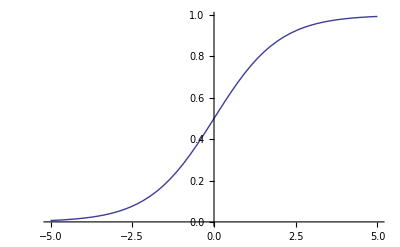

```mathematica
Plot[Logistic[x],{x,-5,5}]
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Sampling Functions

```mathematica
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
zsample[l_]:= (Sign[Thread[l - RandomReal[1, Length[l]]]]+1)/2;
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
HiddenProbabilities[w_][v_]:=Logistic[wᵀ.v];
VisibleProbabilities[w_][h_]:= Most[Logistic[w.h]];
```

#### Learning

```mathematica
ClearAll[DataLearning,DeltaWeight]
```

```mathematica
DeltaWeight[ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew,v3,h3},
wnew=w;
Do[
h1=SampleHidden[w][v1];
v2=SampleVisible[w][h1];
h2=SampleHidden[w][v2];
v3=SampleVisible[w][h2];
h3=SampleHidden[w][v3];
(*
w0=1-Outer[BitXor, v1, h1];
w1=1-Outer[BitXor, v1, h3];*)
w0=Outer[Times, v1, h1];
w1=Outer[Times, v1, h3];

wnew += ϵ*(w0-w1);
,
{16}];
wnew
]
```

```mathematica
DataLearning[w_,ϵ_,n_,dataV_]:=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n]
```

```mathematica
StepLearning[w_,ϵ_,n_,dataV_]:=Module[{w1,w2,w3},w1=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n/3];
w2=Nest[Function[DeltaWeight[ϵ/10,RandomChoice[dataV]][#]],w1,n/3];
w3=Nest[Function[DeltaWeight[ϵ/100,RandomChoice[dataV]][#]],w2,n/3];
w3
]
```

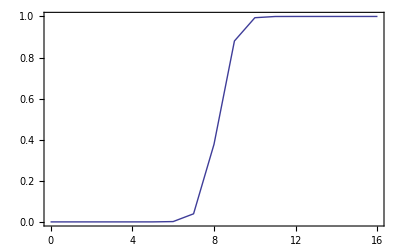

```mathematica
SeedRandom[5];
Hn=1;Vn=17;
W=RandomReal[{-0.5,0.5},{Vn,Hn}];
dataV=Append[#*2-1,1]& /@ {{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}};
w1=StepLearning[W,0.002,4500,dataV];

m=Map[HiddenProbabilities[w1],Append[#,1]& /@Tuples[{-1,1},16]];
m1=Map[HammingDistance[{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},#]&,Tuples[{0,1},16]];
pairs=Transpose[{m1,Flatten[m]}];
pairs2=Mean /@ GatherBy[pairs,First];
ListPlot[Sort[pairs2],PlotRange->{All,{0,1}},PlotRangePadding->0.1,Frame->True,Joined->True]
```

### Quantitative Analysis of addition of noise in learning

A technique to do Supervised learning in Deep Belief nets was developed wherein, each input vector had additional ID bits at the end, to label it. This method was used in the following example:
Starting out with {0,0,0,0,1,1,1,1}-labelled {1} we went till {1,1,1,1,0,0,0,0} -labelled {0}such that at each step one bit was flipped. This was done to do inference on a system already trained on the aforementioned vectors and the inference probabilities were plotted against the distance from the training vectors.
The result plot had sudden spikes which signified that if we flipped more than 2 bits, the system was essentially confused and gave an almost random result.

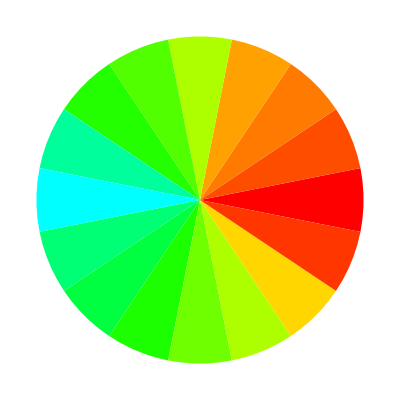

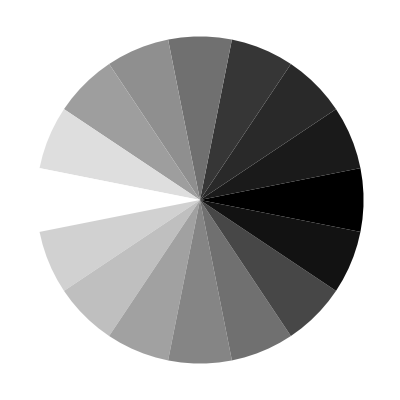

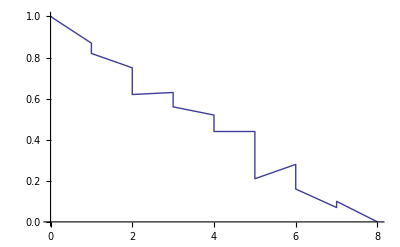

```mathematica
Here is the data plotted in different ways:
```

### Single-layer Deep Learning prototype

Consider the problem of finding the number of bits that are switched on in a given bit vector. The following system had been trained to solve this problem and simulates how the visible layer, the hidden layer and the reconstructed layer of neurons behave.

Here are the code and the simulation:

```mathematica
Logistic[x_]:= 1/(1+Exp[-x]);
sample[l_]:=Sign[Thread[l - RandomReal[1, Length[l]]]];
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
```

```mathematica
weightparity={{-38.484585,2.06403,58.078037,33.865331,-33.30991,56.718331,-3.744155,37.822793,5.433266,-2.178811},{20.124418,19.131588,-47.214679,35.361978,-19.495165,37.233193,-0.421336,47.551539,2.249789,-0.420628},{-30.246488,12.057223,-14.756866,-33.321942,18.730254,-24.272758,5.222581,39.379214,-2.453214,-0.857502},{-26.905716,18.225146,4.275641,47.109465,-21.76953,-26.707435,-0.11133,-42.173073,-0.921316,0.002161},{-22.81645,-34.521089,-6.143066,32.576186,-9.837799,-40.476049,-3.91488,24.633916,-3.785409,-1.192474},{3.190397,1.64981,-6.681031,-10.549223,-13.997248,-5.159975,-3.521171,0.827216,5.567791,2.38286},{2.759137,1.38122,-4.392244,-10.31293,-13.273571,-3.711818,-5.776795,-1.383405,6.957467,1.479063},{3.589532,1.949316,-4.086772,-9.149388,-13.607048,-2.963482,-5.221477,-1.215108,7.118978,0.191266},{1.869047,-0.574278,-5.375689,-7.733936,-13.35842,-4.75254,-5.402653,-0.275095,9.078134,0.002783},{3.286711,0.633152,-4.612389,-10.600392,-13.161066,-4.714219,-6.622172,-1.779608,6.918918,0.010006},{3.429564,4.811952,-0.116047,1.100778,-1.435426,-0.162776,0.478514,-0.218529,-3.675655,-0.071812}};
```

```mathematica
ArrayPlot2[x_] := ArrayPlot[{x+1}/2, Mesh->True, ImageSize-> Length[x] * 20];
```

```mathematica
SetAttributes[EditableArrayPlot,HoldAll];
EditableArrayPlot[sym_Symbol, rest_] := Dynamic[
	ClickPane[ArrayPlot2[sym],(sym⟦Ceiling[First[#]]⟧*=-1;
	rest)&]
];
```

```mathematica
RBMDemo2[V_,W_] := DynamicModule[
	{hidden, visible, reconstruction, auto1 = True, auto2 = True},
	hidden = SampleHidden[W][V];
	visible = V; 
	reconstruction=SampleVisible[W][hidden];
	Dynamic[
		Row[{
			EditableArrayPlot[visible, 
				hidden=SampleHidden[W][visible];
				reconstruction=SampleVisible[W][hidden]], 
				" → ", Checkbox[Dynamic[auto1]],"→ ",
			Dynamic[
				If[auto1, hidden=SampleHidden[W][visible]];
				EditableArrayPlot[hidden, 
					reconstruction=SampleVisible[W][hidden]],
				UpdateInterval -> 0.1
			],
			" → ",Checkbox[Dynamic[auto2]], "→ "
			Dynamic[
				If[auto2, reconstruction=SampleVisible[W][hidden]];
				ArrayPlot2[reconstruction],
				UpdateInterval -> 0.1
			]
		}]
	]
];
```

```mathematica
RBMDemo2[{-1,-1,-1,1,1,-1,1,1,-1,1,1},weightparity]
```

## Demonstrations

## Links/References

en.wikipedia.org/wiki/Boltzmann_machine
www.scholarpedia.org/article/Boltzmann_machine
imonad.com/rbm/restricted-boltzmann-machine/
deeplearning.net/tutorial/rbm.html
www.scholarpedia.org/article/Deep_belief_networks
videolectures.net/mlss09uk_hinton_dbn/
www.cs.toronto.edu/~hinton/absps/fastnc.pdf
en.wikipedia.org/wiki/Hilbert_curve
en.wikipedia.org/wiki/Karnaugh_map
en.wikipedia.org/wiki/Gray_code

Last Modified: Wednesday, July 11, 2012

"Insert date..."